Exact solutions of the Boltzmann equation

Max Krook and Tai Tsun Wu, The Physics of Fluids 20, 1589 (1977)
Notebook: Óscar Amaro, November 2022 @ GoLP-EPP
Contact: oscar.amaro@tecnico.ulisboa.pt

Introduction
In this notebook we reproduce some results from the paper.

```mathematica
(* eq 20 *)
Clear[v,α,ϕ]
ϕ=(2π α)^(-3/2)Exp[-v^2/(2α)]/.{α->1}
4π Integrate[ϕ v^(2n+2),{v,0,∞}]//Normal//Simplify
```

(ⅇ^(-v^2/2))/(2 √2 π^(3/2))

(2^(1+n) Gamma[3/2+n])/(√π)

```mathematica
(* eq 56 is solution to eq 55+  *)
Clear[z,Z,eq]
Z=2(1-z)(1-(1-z)^(1/2));
Z D[Z,z]+5Z-6z(1-z)//Simplify
(* boundary condition eq53 *)
Series[Z,{z,0,1}]
```

0

z+O[z]^2

1/(2 (1-√(1-z)) (1-z))

Log[1-√(1-z)]-1/2 Log[1-z]

-Log[-1+1/(√(1-z))]+Log[1-√(1-z)]-1/2 Log[1-z]

O[z]^14

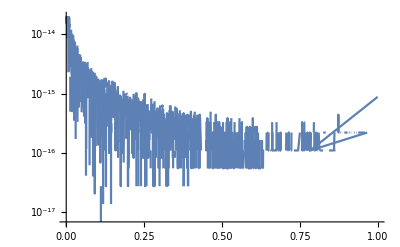

```mathematica
(* eq 57  *)
Clear[z,Z,η,dηdz,int,diff]
Z=2(1-z)(1-(1-z)^(1/2));
dηdz=1/Z
int=Refine[Integrate[dηdz,z]//Simplify,{z>0,z<1}]
diff=int-Log[(1-z)^(-1/2)-1]
(* same result *)
Series[diff,{z,0,13}]
LogPlot[Abs[diff],{z,0,1}]
```

```mathematica
(* prove eq67+ *)
Clear[ζ,n,g]
g=4/Sqrt[π] Sum[Gamma[n+3/2]/((2n)!)ζ^n,{n,0,∞}]
D[g,ζ]//Simplify
```

ⅇ^(ζ/4) (2+ζ)

1/4 ⅇ^(ζ/4) (6+ζ)

```mathematica
(* get eq 69 from Fourier transformed solution *)
Clear[hbar,p,τ,f,v,int,intp,intm,Κ,h,f69]
hbar=(4π)^-1(2+(Κ-3)p^2+Κ(1-Κ)p^4)Exp[-Κ p^2/2];
(* there is a typo in the paper: the complex exponential in the integrand function must be Exp[I p v] and not Exp[I p τ], otherwise h would never be a function of v *)
intp=Refine[1/(2π)Integrate[hbar Exp[I p v],p]//Normal//Expand//Simplify,{p∈Reals,v>0,Κ>0}]//Simplify
intm=intp/.{p->-p}//Simplify;
(* computing the limit would take too much time *)
(*h=((Limit[int,{p->∞}]//Normal//Simplify)-(Limit[int,{p->-∞}]//Normal//Simplify))//Simplify*)

(* int(p) - int(-p) *)
(intp-intm)//FullSimplify

(* the only term that survives p->±∞ is the one containing (because exp(-p^2)->0 *)
I(Limit[Erfi[-ⅈ p],p->∞]-Limit[Erfi[ⅈ p],p->∞])

h=1/(16 π^2 Κ^(7/2))ⅇ^(-v^2/(2 Κ)) v √(2 π) v (v^2-(3+v^2) Κ+5 Κ^2)2//Simplify;

f=1/v^2 h

(* actual distribution *)
f69=Exp[-v^2/(2Κ)]/(2Κ(2π Κ)^(3/2))((5Κ-3)+((1-Κ)/Κ)v^2);

(* check *)
f-f69//Simplify
```

1/(16 π^2 Κ^(7/2))ⅇ^(-(v^2+p^2 Κ^2)/(2 Κ)) (2 ⅇ^((v (v+2 ⅈ p Κ))/(2 Κ)) √Κ (-ⅈ v^3 (-1+Κ)-p v^2 (-1+Κ) Κ+p (2+p^2 (-1+Κ)) Κ^3+ⅈ v Κ (-2-(-4+p^2) Κ+p^2 Κ^2))+ⅈ ⅇ^((p^2 Κ)/2) √(2 π) v^2 (v^2 (-1+Κ)+(3-5 Κ) Κ) Erfi[(v+ⅈ p Κ)/(√2 √Κ)])

1/(16 π^2 Κ^(7/2))ⅇ^(-(v^2+p^2 Κ^2)/(2 Κ)) (4 ⅇ^(v^2/(2 Κ)) p Κ^(3/2) (-v^2 (-1+Κ)+(2+p^2 (-1+Κ)) Κ^2) Cos[p v]+v (ⅈ ⅇ^((p^2 Κ)/2) √(2 π) v (v^2-(3+v^2) Κ+5 Κ^2) (Erfi[(v-ⅈ p Κ)/(√2 √Κ)]-Erfi[(v+ⅈ p Κ)/(√2 √Κ)])-4 ⅇ^(v^2/(2 Κ)) √Κ (-v^2 (-1+Κ)+Κ (-2+(4+p^2 (-1+Κ)) Κ)) Sin[p v]))

2

(ⅇ^(-v^2/(2 Κ)) (v^2-(3+v^2) Κ+5 Κ^2))/(4 √2 π^(3/2) Κ^(7/2))

0

## Fig 1 Analytical solution eq 71

(ⅇ^(1/6 (-(3 v^2)/(1-ⅇ^(-τ/6))+τ)) (5+2 ⅇ^(τ/3)+ⅇ^(τ/6) (-7+v^2)))/(4 √(2-2 ⅇ^(-τ/6)) (-1+ⅇ^(τ/6))^3 π^(3/2))

(ⅇ^(-v^2/2))/(2 √2 π^(3/2))

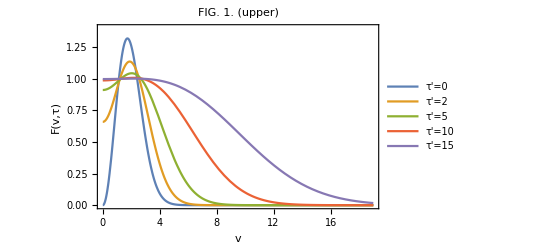

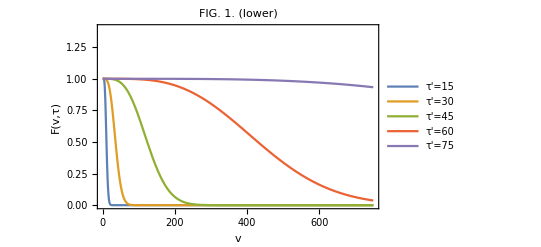

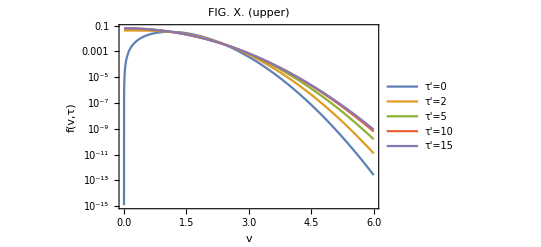

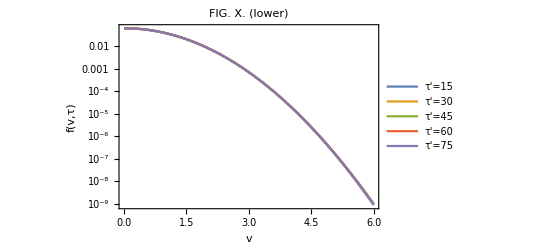

```mathematica
Clear[Κ,τ,F,v,τ]

(* actual distribution *)
f=Exp[-v^2/(2Κ)]/(2Κ(2π Κ)^(3/2))((5Κ-3)+((1-Κ)/Κ)v^2)/.{Κ->1-Exp[-τ/6]}//Simplify

(* asymptotic time solution *)
Limit[f,τ->∞]

(* eq 60 *)
Κ[τ_]:=1-Exp[-τ/6]

(* eq 71 F(v,τ) = f(v,τ)/f(v,∞) *)
F[v_,τ_]:=((5Κ[τ]-3)/(2Κ[τ]^2.5)+(1-Κ[τ])/(2Κ[τ]^3.5)v^2)Exp[-1/2 v^2(1/Κ[τ]-1)]

(* fig 1 *)
Plot[{F[v,0+6Log[5/2]],F[v,2+6Log[5/2]],F[v,5+6Log[5/2]],F[v,10+6Log[5/2]],F[v,15+6Log[5/2]]},{v,0,19},PlotRange->{0,1.4},PlotLabel->"FIG. 1. (upper)", Frame->True,FrameLabel->{"v","F(v,τ)"},PlotLegends->{"τ'=0","τ'=2","τ'=5","τ'=10","τ'=15"}]
Plot[{F[v,15+6Log[5/2]],F[v,30+6Log[5/2]],F[v,45+6Log[5/2]],F[v,60+6Log[5/2]],F[v,75+6Log[5/2]]},{v,0,750},PlotRange->{0,1.4},PlotLabel->"FIG. 1. (lower)", Frame->True,FrameLabel->{"v","F(v,τ)"},PlotLegends->{"τ'=15","τ'=30","τ'=45","τ'=60","τ'=75"}]

(* f(v,τ), figure not included in paper *)
LogPlot[{(f/.{τ->0+6Log[5/2]}),(f/.{τ->2+6Log[5/2]}),(f/.{τ->5+6Log[5/2]}),(f/.{τ->10+6Log[5/2]}),(f/.{τ->15+6Log[5/2]})},{v,0,6},PlotLabel->"FIG. X. (upper)", Frame->True,FrameLabel->{"v","f(v,τ)"},PlotLegends->{"τ'=0","τ'=2","τ'=5","τ'=10","τ'=15"},PlotRange->Automatic
]
LogPlot[{(f/.{τ->15+6Log[5/2]}),(f/.{τ->30+6Log[5/2]}),(f/.{τ->45+6Log[5/2]}),(f/.{τ->60+6Log[5/2]}),(f/.{τ->55+6Log[5/2]})},{v,0,6},PlotLabel->"FIG. X. (lower)", Frame->True,FrameLabel->{"v","f(v,τ)"},PlotLegends->{"τ'=15","τ'=30","τ'=45","τ'=60","τ'=75"},PlotRange->Automatic]
```